VQCDThermo basic tutorial.

This notebook contains the minimal tutorial needed to getting started in computing the black hole solutions to the VQCD equations of motion, and extracting some simple plots and observables from them. You should read the paper arxiv:1312.5199 in order to have some idea on what we’re computing here, and you should have reasonable familiarity with Mathematica syntax.

We assume here that you have already installed the package so that Mathematica can find it. See Readme.md in the repository for instructions. First we need to load the package:

```mathematica
Needs["VQCDThermo`"]
```

Then we need to define some potentials:

```mathematica
xf = 1.;
pots = DefineJKPotIKappaMod[xf]
```

{VQCDThermo`VQCDCore`Private`Vg$1013,VQCDThermo`VQCDCore`Private`Vf$1013,VQCDThermo`VQCDCore`Private`κ$1013,VQCDThermo`VQCDCore`Private`κ$1013}

The function above defines the potentials used in the finite T, finite μ -paper. I gave xf a numerical value 1., since I’ll be wanting to do some calculations.

There are other potential functions in the file VQCDCore.m, and following their example you should also be able to define you own potentials.

The object pots contains a list of the potential functions, specifically {Vg, Vf, κ, ω} defined as pure functions. Let’s just check with Vg that we can for example plot it. This is of course not necessary for just using the potentials for calculations.

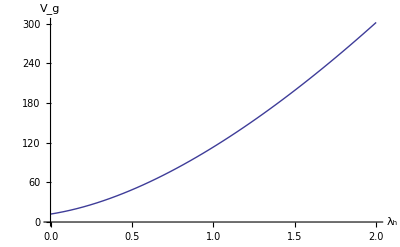

```mathematica
Vg = pots[[1]];
Plot[Vg[λ], {λ, 0, 2}, AxesLabel-> {"λ_h", "V_g"}]
```

Now we’re ready to compute a solution. There are certain limits to the parameter values which lead to a solution, see the paper for more details. Here we of course pick ones which work.

The most logical names for the parameters are protected and reserved, since they are used as indices in thermodynamics datasets, see ThermoAnalysisTutorial.nb. We append v for value in the variable names.

Start off with a zero mass, zero tachyon solution, and just arbitrarily pick nt = 1:

```mathematica
λhv = 1.;
τhv = 0.;
ntv = 1.;
sol1 = SolveAndScaleVQCDBH[λhv, τhv, ntv, pots]
```

{VQCDThermo`VQCDCore`Private`q1$2412,VQCDThermo`VQCDCore`Private`f1$2412,VQCDThermo`VQCDCore`Private`λ1$2412,VQCDThermo`VQCDCore`Private`τd1$2412,VQCDThermo`VQCDCore`Private`τ1$2412,2.7845×10^-9,160.,1.50468,1.89035,True,{3.,3.5},1.40102}

Then let’s take some numbers out of it. Everything is in units of Λ. Note that the code calls the 0-component of the gauge field A, as in A0, as opposed to Φ in the paper.

```mathematica
Tv= TemperatureFromSols[sol1]
{A0, μv} = AAndMuFromSols[sol1, ntv, pots]
s = s4G5FromSols[sol1] (*Entropy density*)
nv = 1/(4Pi)ntildeFromSols[sol1, ntv] (*Charge density, in units of Subscript[ℒ, A]*)
```

0.334427

{Function[A$,VQCDThermo`VQCDCore`Private`Afunc$2479[A$]-VQCDThermo`VQCDCore`Private`Afunc$2479[2.7845×10^-9]],0.0976164}

0.293538

0.023359

We can also plot the field configurations. It’s a bit clearer to assign names to the fields before starting to work. Unfortunately, using for example λ as a name for the λ-field can cause conflicts in any further attempts to solve the system, so append s for solution to all field names.

All the fields and components of the metric are returned as functions of A = log(b). The radial coordinate z as a function of A can be obtained from the function zFromSols.

The warnings are due to a well known Mathematica bug (fixed in v9): http://mathematica.stackexchange.com/questions/5986/why-does-loglinearplot-sample-its-argument-outside-the-specified-domain

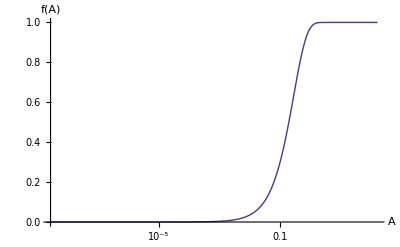

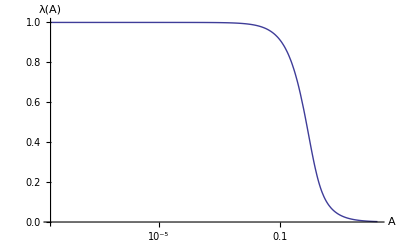

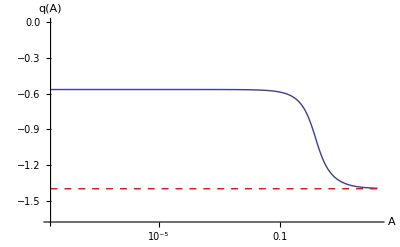

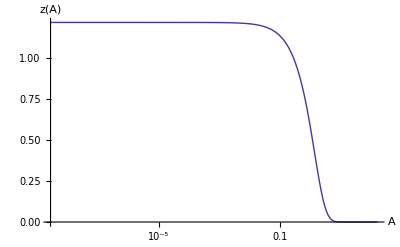

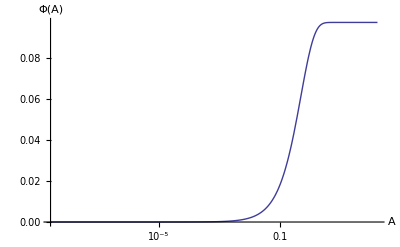

```mathematica
λs = λFromSols[sol1];
fs = fFromSols[sol1];
qs = qFromSols[sol1];
τs = τFromSols[sol1];
{Amin, Amax} = ARangeFromSols[sol1];
zs = zFromSols[sol1];

{bcoefs, ell} = bCoefsFromPotential[pots]; (*Extract Subscript[ℒ, UV] to check the correct asymptotic of q*)

LogLinearPlot[fs[A], {A, Amin, Amax}, AxesLabel-> {"A", "f(A)"}]
LogLinearPlot[λs[A], {A, Amin, Amax}, AxesLabel -> {"A", "λ(A)"}]
LogLinearPlot[{qs[A], -ell}, {A, Amin, Amax}, AxesLabel -> {"A", "q(A)"}, PlotStyle-> {Automatic, {Red, Dashed}}, PlotRange-> {Min[-ell, qs[Amax]]*1.2, 0}]

LogLinearPlot[zs[A], {A, Amin, Amax}, AxesLabel-> {"A", "z(A)"}]

LogLinearPlot[A0[A], {A, Amin, Amax},  AxesLabel -> {"A", "Φ(A)"}]
```

Let’s then try looking at finite τ solutions:

```mathematica
λhv = 2.;
τhv = 1.;
ntv = 1.;
sol2a = SolveAndScaleVQCDBH[λhv, τhv, ntv, pots]
```

{VQCDThermo`VQCDCore`Private`q1$4541,VQCDThermo`VQCDCore`Private`f1$4541,VQCDThermo`VQCDCore`Private`λ1$4541,VQCDThermo`VQCDCore`Private`τd1$4541,VQCDThermo`VQCDCore`Private`τ1$4541,3.4564×10^-9,160.,1.82076,1.71861,True,{3.,3.5},1.40102}

Check the mass

```mathematica
QuarkMass[sol2a, pots]
```

0.765867

All good, but we’d usually rather fix the mass, and determine τh from that. This will take a minute or two:

```mathematica
mq = 0;
τhv = τhFromQuarkMass[mq, λhv, ntv, pots]
```

0.358889

Now we can use that value to compute a solution. Note that the τh we gained is of course only correct for this specific set of λh, nt, and needs to be recomputed for other values. This is the primary effort in terms of computation time for the thermo solutions.

Let’s now compute the solution corresponding to that.

```mathematica
sol2 = SolveAndScaleVQCDBH[λhv, τhv, ntv, pots];
```

The corresponding observables are

```mathematica
Tv = TemperatureFromSols[sol2]
{A0, μv} = AAndMuFromSols[sol2, ntv, pots]
s = s4G5FromSols[sol2] (*Entropy density*)
nv = 1/(4Pi)ntildeFromSols[sol2, ntv] (*Charge density, in units of Subscript[ℒ, A]*)
mqactual = QuarkMass[sol2, pots] (*The actual mass*)
```

0.144471

{Function[A$,VQCDThermo`VQCDCore`Private`Afunc$33422[A$]-VQCDThermo`VQCDCore`Private`Afunc$33422[2.82491×10^-9]],0.0350492}

0.00767148

0.000610477

2.58533×10^-12

Note that the mass is indeed of order 10^-12.

Let’s see how the configurations appear:

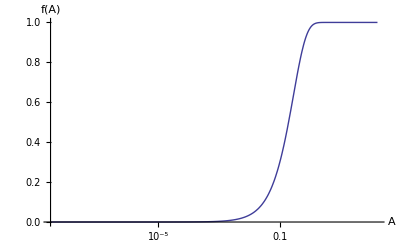

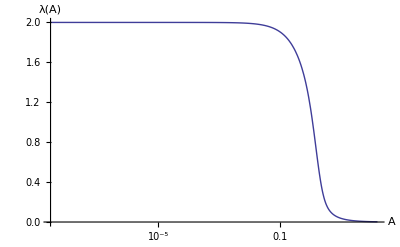

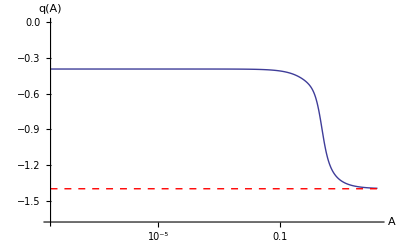

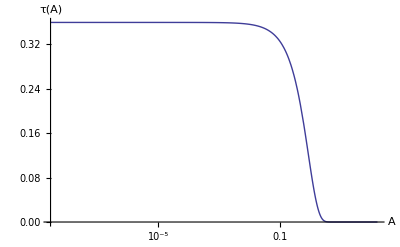

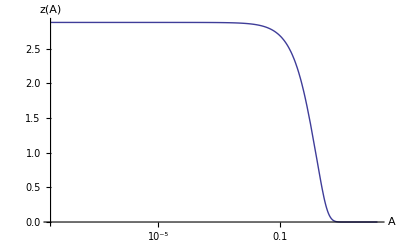

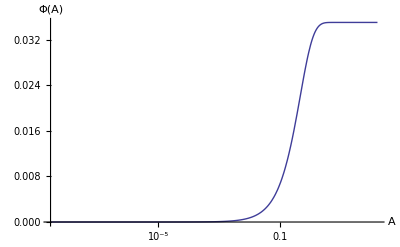

```mathematica
λs = λFromSols[sol2];
fs = fFromSols[sol2];
qs = qFromSols[sol2];
τs = τFromSols[sol2];
{Amin, Amax} = ARangeFromSols[sol2];
zs = zFromSols[sol2];

{bcoefs, ell} = bCoefsFromPotential[pots]; (*Extract Subscript[ℒ, UV] to check the correct asymptotic of q*)

LogLinearPlot[fs[A], {A, Amin, Amax}, AxesLabel-> {"A", "f(A)"}]
LogLinearPlot[λs[A], {A, Amin, Amax}, AxesLabel -> {"A", "λ(A)"}]
LogLinearPlot[{qs[A], -ell}, {A, Amin, Amax}, AxesLabel -> {"A", "q(A)"}, PlotStyle-> {Automatic, {Red, Dashed}}, PlotRange-> {Min[-ell, qs[Amax]]*1.2, 0}]
LogLinearPlot[τs[A], {A, Amin, Amax}, AxesLabel-> {"A", "τ(A)"}]

LogLinearPlot[zs[A], {A, Amin, Amax}, AxesLabel-> {"A", "z(A)"}]

LogLinearPlot[A0[A], {A, Amin, Amax},  AxesLabel -> {"A", "Φ(A)"}]
```

Finally, let’s see how some of these components can be combined to find, as an exercise, a point very near to the AdS2 -limit, with μ = 0.507, that is, very close to T = 0 chiral restoration transition.

Find by finding the exact position of the AdS2 -point. This is of course given in the paper, so this here is just an example.

```mathematica
ntcritfun = ntCritical[pots]; (*This returns the limiting curve nt(la) where Veff = 0*)
λhcrit = λhcr /. FindRoot[ntcritfun'[λhcr], {λhcr, 1.5, 0.5}, Method-> "Brent"] (**)
ntcrit = ntcritfun[λhcrit]
ntv = ntcrit - 10^-2
```

1.10794

12.2947

12.2847

We’ll be looking at 10^-2 away from the AdS2 -point

Then define a function which returns just the μ given λh

```mathematica
μNearAdS2[λh_?NumericQ] := Module[{sol}, 
sol = SolveAndScaleVQCDBH[λh, 0, ntv, pots];
AAndMuFromSols[sol, ntv, pots][[2]] (*Index 2 is μ*)
]
```

Now, we need to find an interval in λh where to look for this. It would be easy enough to guess, but let’s do it systematically.

FindNumLimit is a helper function in NumericsExtra, which does a binary search for the point where a function ceases to have a numeric value (as judged by NumericQ).

```mathematica
λhmax = FindNumLimit[μNearAdS2[λhv], {λhv, λhcrit, 2.}]
λhmin = FindNumLimit[μNearAdS2[λhv], {λhv, 0.01, λhcrit}]
```

1.16078

1.05126

Check that this interval brackets the value of μ we’re looking for. Then we can just use Mathematica’s standard FindRoot with Brent’s method to find the λ_h we want:

```mathematica
μNearAdS2[λhmax]
μNearAdS2[λhmin]
```

0.0583201

2.85426

It does.

```mathematica
λhμc = λhv /. FindRoot[μNearAdS2[λhv] == 0.507, {λhv, λhmin, λhmax}, Method -> "Brent"]
```

1.15969

The FindRoot warning just means that this is as close as we can get without using more than machine precision. Compute the actual solution, the observables, and plot the configurations.

```mathematica
solμc = SolveAndScaleVQCDBH[λhμc, 0, ntv, pots]

Tv = TemperatureFromSols[solμc]
{A0, μv} = AAndMuFromSols[solμc, ntv, pots]
s = s4G5FromSols[solμc] (*Entropy density*)
nv = 1/(4Pi)ntildeFromSols[solμc, ntv] (*Charge density, in units of Subscript[ℒ, A]*)
```

{VQCDThermo`VQCDCore`Private`q1$61765,VQCDThermo`VQCDCore`Private`f1$61765,VQCDThermo`VQCDCore`Private`λ1$61765,VQCDThermo`VQCDCore`Private`τd1$61765,VQCDThermo`VQCDCore`Private`τ1$61765,9.8691×10^-13,160.,3.78263,0.0128834,True,{3.,3.5},1.40102}

0.0000239713

{Function[A$,VQCDThermo`VQCDCore`Private`Afunc$61766[A$]-VQCDThermo`VQCDCore`Private`Afunc$61766[9.8691×10^-13]],0.507}

0.0184764

0.0180623

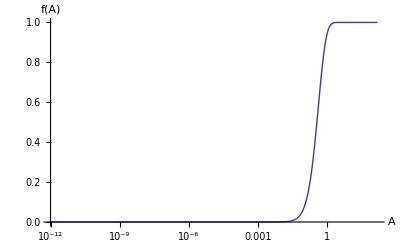

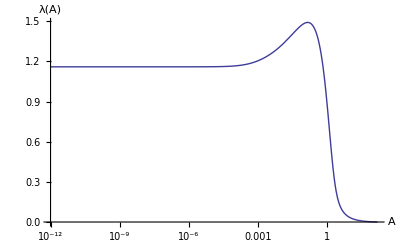

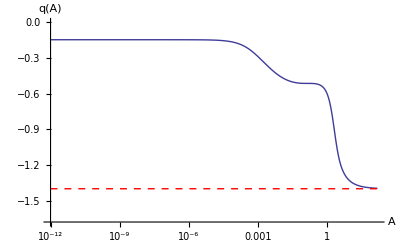

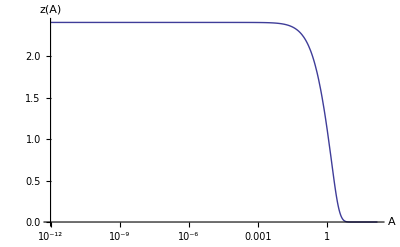

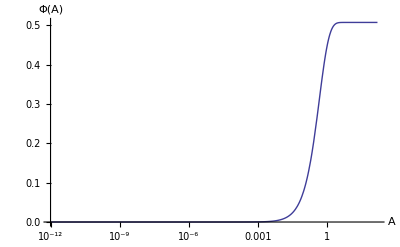

```mathematica
λs = λFromSols[solμc];
fs = fFromSols[solμc];
qs = qFromSols[solμc];
τs = τFromSols[solμc];
{Amin, Amax} = ARangeFromSols[solμc];
zs =zFromSols[solμc];

{bcoefs, ell} = bCoefsFromPotential[pots]; (*Extract Subscript[ℒ, UV] to check the correct asymptotic of q*)

LogLinearPlot[fs[A], {A, Amin, Amax}, AxesLabel-> {"A", "f(A)"}]
LogLinearPlot[λs[A], {A, Amin, Amax}, AxesLabel -> {"A", "λ(A)"}, PlotRange-> All]
LogLinearPlot[{qs[A], -ell}, {A, Amin, Amax}, AxesLabel -> {"A", "q(A)"}, PlotStyle-> {Automatic, {Red, Dashed}}, PlotRange-> {Min[-ell, qs[Amax]]*1.2, 0}]

LogLinearPlot[zs[A], {A, Amin, Amax}, AxesLabel-> {"A", "z(A)"}]

LogLinearPlot[A0[A], {A, Amin, Amax},  AxesLabel -> {"A", "Φ(A)"}]
```

Here’s how to plot, for example, λ(z):

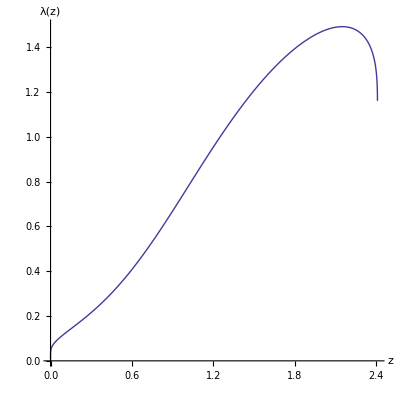

```mathematica
ParametricPlot[{zs[A], λs[A]}, {A, Amin, 50}, AspectRatio -> 1, PlotPoints-> 1500, PlotRange-> {{0, zs[Amin]}, All}, AxesLabel-> {"z", "λ(z)"}]
```

That’s all for now, folks! Check out the thermo tutorials too!